Plot::exclul: {Im[0.041470123456790124` x^2 + 1.` x^4 + 0.0030864197530864196` d12[Times[« 2 »], 0]^2] - 0} must be a list of equalities or real-valued functions.

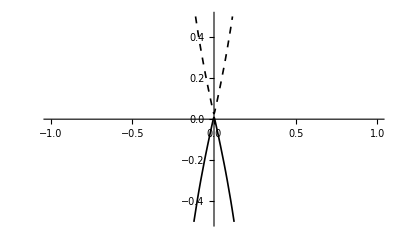

Plot3D::exclul: {Im[0.041470123456790124` x^2 + 1.` x^4 + 0.0010244444444444444` y^2 + 2.` x^2 y^2 + 1.` y^4 + 0.0030864197530864196` d12[Times[« 2 »], Times[« 2 »]]^2] - 0} must be a list of equalities or real-valued functions.

-Graphics3D-

```mathematica
Clear["Global`*"]
A=-3.62; B=-18; C1=0.018;D1=-0.594; M=0.00922;
A1=-3.42; B1=-16.9; C21=-0.0263;D21=0.514; M11=-0.00686;
d1[x_,y_]=A*x;
d2[x_,y_]=A*y;
d3[x_,y_]=M-B*(x^2+y^2);
e1[x_,y_]=C1-D1*(x^2+y^2);
M1={{e1[x,y]+d3[x,y],d1[x,y]-I*d2[x,y],0,0},{d1[x,y]+I*d2[x,y],e1[x,y]-d3[x,y],0,0},{0,0,e1[x,y]+d3[x,y],d1[-x,-y]-I*d12[-x,-y]},{0,0,d1[-x,-y]+I*d12[-x,-y],e1[x,y]-d3[x,y]}};
A=Eigenvalues[M1];
F1[x_,y_]=A[[1]]; F2[x_,y_]=A[[2]]; F3[x_,y_]=A[[3]];F4[x_,y_]=A[[4]];
Plot[{F1[x,0],F2[x,0],F3[x,0],F4[x,0]},{x,-1,1},PlotRange->{-0.5,0.5}, PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Green},{Thickness[0.003],Green, Dashed}}]
Plot3D[{F1[x,y],F2[x,y],F3[x,y],F4[x,y]},{x,-1,1},{y,-1,1},PlotRange->{-0.5,0.5}]
```